```mathematica
(* Import a pacakge (.m file)... equivalent of #include in C++ *)
Import["proj2helpers.m"];
```

```mathematica
(* Constructing Lists using Table*)
threes = Table[3,{5}]
alist = Table[i,{i,8}]
alolon = Table[ 3*(i-1)+j,{i,4},{j,3}]
```

{3,3,3,3,3}

{1,2,3,4,5,6,7,8}

{{1,2,3},{4,5,6},{7,8,9},{10,11,12}}

```mathematica
(* Single Element Selection *)
alist[[3]]
{4,52,3,6}[[2]]
alolon[[4,2]]
```

3

52

11

```mathematica
(* Multi Element Selection *)
alist[[{1,3,5}]]
alist[[{3,5,1}]]
{4,52,3,6}[[Table[2,{10}]]]
```

{1,3,5}

{3,5,1}

{52,52,52,52,52,52,52,52,52,52}

```mathematica
(* Multi Element Selection with Spans *)
blist = Table[20-i,{i,1,20}]
blist[[1;;5]]
blist[[6;;]]
blist[[;;10]]
blist[[;;]]
blist[[20;;1;;-1]]
blist[[1;;20;;3]]
```

{19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,0}

{19,18,17,16,15}

{14,13,12,11,10,9,8,7,6,5,4,3,2,1,0}

{19,18,17,16,15,14,13,12,11,10}

{19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,0}

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

{19,16,13,10,7,4,1}

```mathematica
(* Selecting from 2D/Table like Lists *)
alolon[[2]]
alolon[[;;,1]]
alolon[[1;;2,{1,3}]]
```

{4,5,6}

{1,4,7,10}

{{1,3},{4,6}}

```mathematica
mytab=Table[10*i+j,{i,0,19},{j,0,9}]
```

{{0,1,2,3,4,5,6,7,8,9},{10,11,12,13,14,15,16,17,18,19},{20,21,22,23,24,25,26,27,28,29},{30,31,32,33,34,35,36,37,38,39},{40,41,42,43,44,45,46,47,48,49},{50,51,52,53,54,55,56,57,58,59},{60,61,62,63,64,65,66,67,68,69},{70,71,72,73,74,75,76,77,78,79},{80,81,82,83,84,85,86,87,88,89},{90,91,92,93,94,95,96,97,98,99},{100,101,102,103,104,105,106,107,108,109},{110,111,112,113,114,115,116,117,118,119},{120,121,122,123,124,125,126,127,128,129},{130,131,132,133,134,135,136,137,138,139},{140,141,142,143,144,145,146,147,148,149},{150,151,152,153,154,155,156,157,158,159},{160,161,162,163,164,165,166,167,168,169},{170,171,172,173,174,175,176,177,178,179},{180,181,182,183,184,185,186,187,188,189},{190,191,192,193,194,195,196,197,198,199}}

```mathematica
tab =  TableForm[mytab,TableHeadings->
{Table[i,{i,20}],{"a","b","c","d","e","f","g","h","i","j"}}];
capped = 
Labeled[tab,
"Table 1: Some data showing some relationship",Spacings->{Automatic,2}]
```

| a | b | c | d | e | f | g | h | i | j
1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
2 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
3 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29
4 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
5 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49
6 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59
7 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69
8 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79
9 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89
10 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99
11 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109
12 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119
13 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129
14 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139
15 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149
16 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159
17 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169
18 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179
19 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189
20 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199Table 1: Some data showing some relationship

```mathematica
Export["TimesTable.svg",capped]
```

TimesTable.svg

```mathematica
(*Random Table *)
randtab = RandomVariate[NormalDistribution[],{20,10}];
TableForm[randtab]
```

-0.119453 | 0.585041 | -1.52268 | -1.34356 | -0.66727 | 1.0222 | 0.0775642 | -0.690355 | 0.805926 | -0.012155
-0.77578 | 0.11147 | 0.77157 | -1.74814 | 0.241801 | 0.239232 | 0.964717 | -1.47192 | 0.786029 | 1.09937
0.261086 | 0.951121 | 0.464777 | -1.11323 | -1.25623 | -0.950666 | 0.795496 | 0.190148 | 0.326627 | -0.608476
0.0381955 | 0.560185 | -0.179037 | 1.13892 | -0.441393 | -0.818812 | 0.861361 | -0.76194 | 1.10747 | 0.359187
0.660111 | 0.971533 | 1.41558 | 1.80397 | 1.85514 | 1.33027 | -0.065919 | -0.20439 | 1.36755 | -0.0238878
0.134043 | 0.889833 | -1.24461 | 0.249797 | -0.877107 | -1.27899 | -0.983105 | -0.550451 | 1.14579 | 0.952609
-0.369567 | 0.140786 | 0.532303 | -0.787218 | 1.07568 | 0.794038 | 1.04829 | 0.81551 | 0.703356 | -1.48424
0.706125 | 1.56969 | 1.16262 | -0.312456 | -0.753766 | -1.25991 | 1.13798 | 0.399563 | -0.663026 | -0.235101
0.36476 | 0.204804 | 0.783984 | -0.322631 | -1.0142 | -0.441907 | 1.2222 | -0.269492 | -1.52719 | 2.1948
-0.217357 | 0.201924 | -0.25413 | 0.0520273 | -1.11365 | -0.878906 | -1.09936 | 1.31138 | -1.03864 | -1.09589
-1.73845 | -0.576916 | -1.7113 | 1.38805 | -1.99818 | -0.908315 | -0.758563 | 0.438743 | 1.12975 | -0.166791
-0.457243 | 0.896052 | 1.05585 | -0.64702 | -1.2455 | -1.79771 | 2.12709 | 0.00238638 | 1.08896 | -0.565269
-0.0215368 | 1.64916 | 0.704845 | -0.737053 | 0.842443 | -0.863073 | -0.441185 | 0.936769 | -0.173706 | -0.182089
1.16739 | 0.102094 | 0.198608 | 0.434973 | 0.0798639 | -0.19493 | 0.72145 | -0.70205 | -0.143257 | 1.79539
0.389533 | -0.517956 | -1.06046 | 0.00517623 | 0.365211 | 0.586188 | -0.603038 | -0.864194 | 0.485404 | 0.372099
-0.873732 | -0.183756 | 0.0765874 | 0.442087 | 1.83694 | -0.440914 | -0.00389554 | 0.390033 | -1.24046 | -0.978323
-1.25364 | -0.221175 | -0.640465 | 0.109394 | -1.90997 | -0.208486 | 1.41356 | 0.0730865 | -0.928295 | 0.181043
1.06589 | 0.304663 | -0.892842 | -0.878339 | 0.0228433 | 1.10231 | 1.169 | -1.22361 | -1.62874 | 0.480912
-2.25607 | -0.519754 | 0.441342 | 0.813159 | 0.0225821 | -0.288093 | 1.37446 | -0.84396 | 0.547309 | -1.19562
-1.0156 | -0.699674 | -1.21715 | 0.155873 | 0.217887 | -0.197175 | 0.286765 | 0.9136 | -0.751079 | 0.277032

```mathematica
(* Min/max for the whole table, by row, then by Column *)
Min[randtab]
Max[randtab]
Map[Min,randtab]
Map[Max,randtab]
Map[Min,Transpose[randtab]]
Map[Max,Transpose[randtab]]
```

-2.25607

2.1948

{-1.52268,-1.74814,-1.25623,-0.818812,-0.20439,-1.27899,-1.48424,-1.25991,-1.52719,-1.11365,-1.99818,-1.79771,-0.863073,-0.70205,-1.06046,-1.24046,-1.90997,-1.62874,-2.25607,-1.21715}

{1.0222,1.09937,0.951121,1.13892,1.85514,1.14579,1.07568,1.56969,2.1948,1.31138,1.38805,2.12709,1.64916,1.79539,0.586188,1.83694,1.41356,1.169,1.37446,0.9136}

{-2.25607,-0.699674,-1.7113,-1.74814,-1.99818,-1.79771,-1.09936,-1.47192,-1.62874,-1.48424}

{1.16739,1.64916,1.41558,1.80397,1.85514,1.33027,2.12709,1.31138,1.36755,2.1948}

```mathematica
(* Mean by Row and Column *)
```

```mathematica
Mean[Transpose[randtab]]
Mean[randtab]
```

{-0.186474,0.0218353,-0.0939349,0.186413,0.910995,-0.156219,0.246894,0.175171,0.119513,-0.413261,-0.490197,0.0457606,0.171458,0.345953,-0.084204,-0.097543,-0.338494,-0.0477902,-0.190464,-0.202952}

{-0.215565,0.320956,-0.0557298,-0.0648115,-0.235844,-0.272682,0.462244,-0.105557,0.069989,0.0582299}

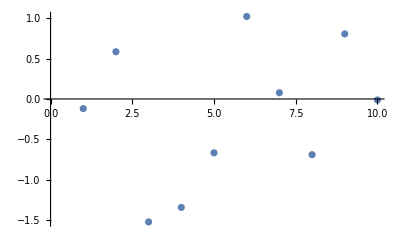

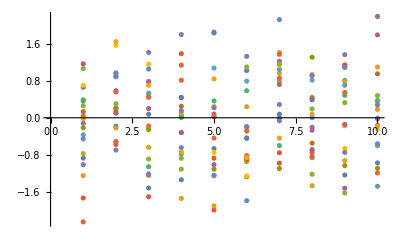

```mathematica
ListPlot[randtab[[1]]]
ListPlot[randtab]
```

```mathematica
xs=Table[10*i,{i,10}]
```

{10,20,30,40,50,60,70,80,90,100}

```mathematica
Transpose[{xs,randtab[[1]]}]
```

{{10,-0.119453},{20,0.585041},{30,-1.52268},{40,-1.34356},{50,-0.66727},{60,1.0222},{70,0.0775642},{80,-0.690355},{90,0.805926},{100,-0.012155}}

```mathematica
Zip[xs_,ys_]:=Transpose[{xs,ys}]
```

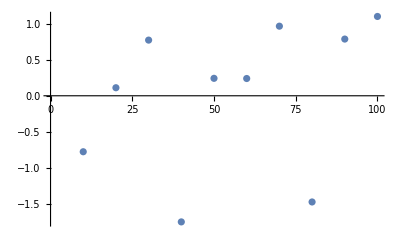

```mathematica
points=Zip[xs,randtab[[2]]];
ListPlot[points]
```

```mathematica
MakePoints[xs_,ytab_] :=
Map[Zip[Table[xs[[#]],{i,Length[ytab[[#]]]}],ytab[[#]] ]&,Table[i,{i,Length[ytab]}]]
```

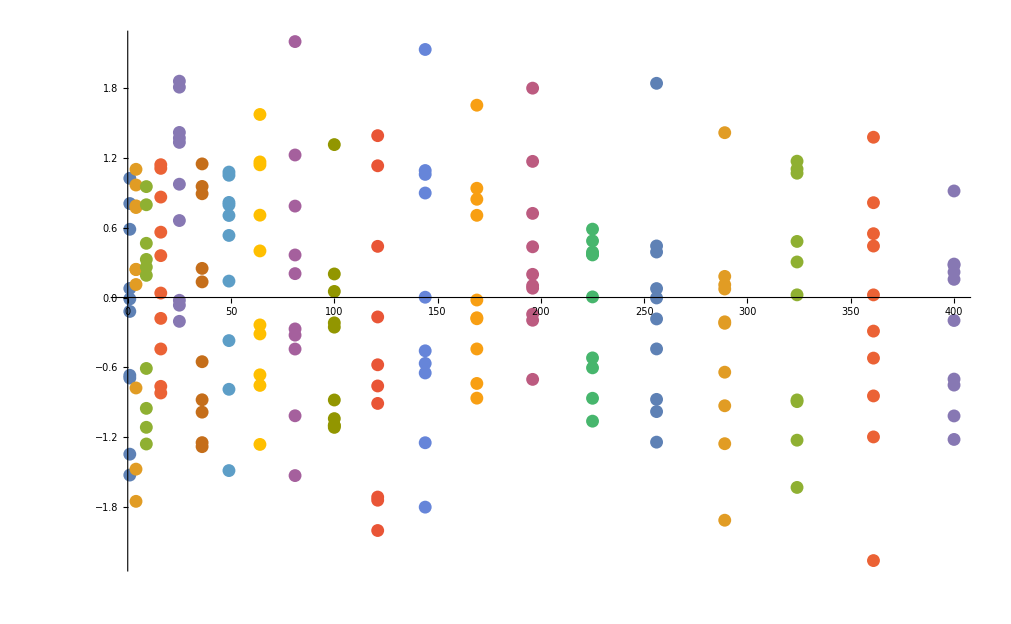

```mathematica
morepoints = MakePoints[Table[i^2,{i,Length[randtab]}],randtab];
ListPlot[morepoints]
```

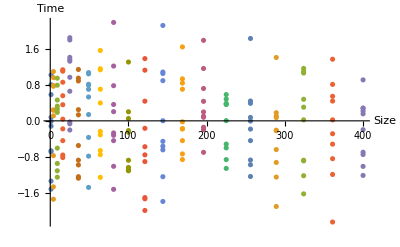

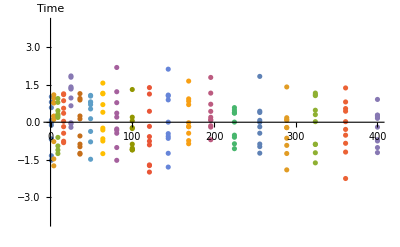

```mathematica
ListPlot[morepoints,AxesLabel->{"Size","Time"},PlotRange->All]
ListPlot[morepoints,AxesLabel->{None,"Time"},PlotRange->{-4,4}]
```

```mathematica
mypoints=Labeled[ListPlot[morepoints,AxesLabel->{"Size","Time"},PlotRange->All],"Figure 2: Size and Time...",Spacings->{Automatic,2}]
Export["datapoints.svg",mypoints]
```

-Graphics-Figure 2: Size and Time...

datapoints.svg